## G=5 models

### Setup

```mathematica
SetDirectory@ParentDirectory@NotebookDirectory[];
<<QuiverGaugeTheory`
<<InterfaceM2`
```

```mathematica
Get@FileNameJoin[{NotebookDirectory[],"functions.wl"}]
$ImportData=True;
$DataDirectory=FileNameJoin[{NotebookDirectory[],"data"}];
$FiguresDirectory=FileNameJoin[{NotebookDirectory[],"figures"}];
```

### Model 11: PdP_2

```mathematica
WPdP2=Subscript[X, 1][1,2]·Subscript[X, 1][2,5]·Subscript[X, 2][5,1]-Subscript[X, 1][1,2]·Subscript[X, 2][2,5]·Subscript[X, 1][5,1]-Subscript[X, 1][1,3]·Subscript[X, 1][3,2]·Subscript[X, 1][2,1]+Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,1]-Subscript[X, 1][1,4]·Subscript[X, 1][4,5]·Subscript[X, 2][5,1]+Subscript[X, 1][3,2]·Subscript[X, 2][2,5]·Subscript[X, 1][5,3]+Subscript[X, 1][1,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,1]-Subscript[X, 1][2,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2];
```

```mathematica
PdP2=Model["PdP2","Descriptions"->{"PdP_2"},"Potential"->WPdP2,"QuiverPositioning"->{2,5,1,3,4}];
```

### Model 12: dP_2

```mathematica
WdP2PhaseA=-(Subscript[X, 1][1,3]·Subscript[X, 1][3,2]·Subscript[X, 1][2,1])+Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,1]+Subscript[X, 1][3,2]·Subscript[X, 2][2,5]·Subscript[X, 1][5,3]-Subscript[X, 1][1,4]·Subscript[X, 2][4,2]·Subscript[X, 2][2,5]·Subscript[X, 1][5,1]-Subscript[X, 1][2,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]+Subscript[X, 1][1,3]·Subscript[X, 1][3,4]·Subscript[X, 2][4,2]·Subscript[X, 1][2,5]·Subscript[X, 1][5,1];
```

```mathematica
WdP2PhaseB=Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,1]-Subscript[X, 1][1,4]·Subscript[X, 2][4,2]·Subscript[X, 2][2,1]-Subscript[X, 1][1,5]·Subscript[X, 1][5,2]·Subscript[X, 3][2,1]+Subscript[X, 1][1,5]·Subscript[X, 2][5,2]·Subscript[X, 2][2,1]-Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]+Subscript[X, 1][2,3]·Subscript[X, 1][3,5]·Subscript[X, 1][5,2]+Subscript[X, 1][1,3]·Subscript[X, 1][3,4]·Subscript[X, 2][4,2]·Subscript[X, 3][2,1]-Subscript[X, 1][1,3]·Subscript[X, 1][3,5]·Subscript[X, 2][5,2]·Subscript[X, 1][2,1];
```

```mathematica
dP2PhaseA=Model[{"dP2","PhaseA"},"Potential"->WdP2PhaseA,"QuiverPositioning"->{4,2,5,1,3}];
dP2PhaseB=Model[{"dP2","PhaseB"},"Potential"->WdP2PhaseB,"QuiverPositioning"->{1,3,{4,5},2}];
```

## Deformations

### PdP_2 ⟹ dP_2 (a)

#### Deformation 1: (1→2→1) – (3→4→5→3)

```mathematica
PdP2def1η=Subscript[X, 1][1,3]·Subscript[X, 1][3,2]·Subscript[X, 2][2,5]·Subscript[X, 1][5,1];
δWPdP2def1=μ (Subscript[X, 1][1,2]·Subscript[X, 1][2,1]-Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]);
WPdP2def1=WPdP2+δWPdP2def1;
```

```mathematica
WPdP2def1Min=WPdP2def1//IntegrateOutMassTerms//Expand
```

-(X_1[1,4]·X_1[4,5]·X_2[5,1])+X_1[3,2]·X_2[2,5]·X_1[5,3]-μ X_1[3,4]·X_1[4,5]·X_1[5,3]+(X_1[1,3]·X_1[3,2]·X_1[2,5]·X_2[5,1])/μ-(X_1[1,3]·X_1[3,2]·X_2[2,5]·X_1[5,1])/μ+X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]-(X_1[1,4]·X_1[4,2]·X_1[2,5]·X_2[5,1])/μ+(X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1])/μ-X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]

```mathematica
RedefChoice1={Subscript[γ, 1][5,3]->0,Subscript[γ, 1][4,5]->0,Subscript[β, 1][5,3]->1/μ,Subscript[β, 1][4,5]->-1/μ,Subscript[α, 1][5,3]->-1/μ,Subscript[α, 1][4,5]->1/μ};
RedefRules1=FieldRedefinition[{Subscript[X, 1][4,5],Subscript[X, 1][5,3]},Quiver[PdP2],2]//.RedefChoice1;
RedefRules1Mass={Subscript[X, 1][3,4]->μ Subscript[X, 1][3,4],Subscript[X, 1][1,4]->μ Subscript[X, 1][1,4],Subscript[X, 1][3,2]->μ Subscript[X, 1][3,2]};
RedefRules1//Column
RedefRules1Mass//Column
```

X_1[4,5]→-(X_1[4,2]·X_1[2,5])/μ+X_1[4,5]/μ
X_1[5,3]→(X_1[5,1]·X_1[1,3])/μ-X_1[5,3]/μ

X_1[3,4]→μ X_1[3,4]
X_1[1,4]→μ X_1[1,4]
X_1[3,2]→μ X_1[3,2]

```mathematica
DG[FieldCases[RedefRules1]/.RedefRules1,{FieldCases[RedefRules1]}]/.{Untrace->1}//Det
```

-1/μ^2

```mathematica
WdP2AFromDef1=Simplify[(WPdP2def1Min/.RedefRules1/.RedefRules1Mass)]
```

-(X_1[1,4]·X_1[4,5]·X_2[5,1])-X_1[3,2]·X_2[2,5]·X_1[5,3]+X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[1,3]·X_1[3,2]·X_1[2,5]·X_2[5,1]+X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]-X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]

```mathematica
Simplify[μ WPdP2def1Min/.RedefRules1[[2]]]//ReplaceAll[{Subscript[X, 1][1,4]->1/μ Subscript[X, 1][1,4],Subscript[X, 1][3,4]->1/μ Subscript[X, 1][3,4],Subscript[X, 1][5,1]->μ Subscript[X, 1][5,1]}]
WdP2AFromDef1+ν Total@ZigZagOperator[WdP2AFromDef1][PdP2def1η]//Simplify//Expand
Collect[%-%%,_CenterDot,Highlighted]
```

-(X_1[1,4]·X_1[4,5]·X_2[5,1])-X_1[3,2]·X_2[2,5]·X_1[5,3]+X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[1,3]·X_1[3,2]·X_1[2,5]·X_2[5,1]-(X_1[1,4]·X_1[4,2]·X_1[2,5]·X_2[5,1])/μ+X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]+(X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2])/μ-X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]

-(X_1[1,4]·X_1[4,5]·X_2[5,1])-X_1[3,2]·X_2[2,5]·X_1[5,3]+X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[1,3]·X_1[3,2]·X_1[2,5]·X_2[5,1]-ν X_1[1,4]·X_1[4,2]·X_1[2,5]·X_2[5,1]+X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]+ν X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]-X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]

X_1[1,4]·X_1[4,2]·X_1[2,5]·X_2[5,1] 1/μ-ν+X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2] -1/μ+ν

```mathematica
WdP2AFromDef1+1/μ Total@ZigZagOperator[WdP2AFromDef1][PdP2def1η]//
ReplaceAll[{Subscript[X, 1][4,5]->Subscript[X, 1][4,5]-1/μ Subscript[X, 1][4,2]·Subscript[X, 1][2,5]}]//Simplify
```

-(X_1[1,4]·X_1[4,5]·X_2[5,1])-X_1[3,2]·X_2[2,5]·X_1[5,3]+X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[1,3]·X_1[3,2]·X_1[2,5]·X_2[5,1]+X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]-X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]

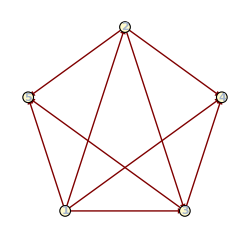
-Graphics--Graphics-

X_1[1,3]·X_1[3,2]·X_1[2,1] 1-a+X_1[1,4]·X_2[4,2]·X_2[2,5]·X_1[5,1] 1-a+X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2] 1-a+X_1[1,4]·X_1[4,2]·X_1[2,1] -1+a+X_1[3,2]·X_2[2,5]·X_1[5,3] -1+a+X_1[1,3]·X_1[3,4]·X_2[4,2]·X_1[2,5]·X_1[5,1] -1+a

```mathematica
Row@{
QuiverGraph[dP2PhaseA],
WdP2AFromDef1/.ChangeGroupIndices[{5,4,1,3,2}]/.{Subscript[X, 1][4,2]->Subscript[X, 2][4,2],Subscript[X, 2][4,2]->Subscript[X, 1][4,2]}//Expand//QuiverGraph[{4,2,5,1,3},#]&
}
WdP2AFromDef1/.ChangeGroupIndices[{5,4,1,3,2}]/.{Subscript[X, 1][4,2]->Subscript[X, 2][4,2],Subscript[X, 2][4,2]->Subscript[X, 1][4,2]}//Expand@Collect[Expand[#]+a W[dP2PhaseA]//Simplify,_CenterDot,Highlighted]&
```

## Mesonic branch

### Model 11: PdP_2

```mathematica
PdP2FieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP2,5];
```

```mathematica
PdP2FieldGenRules=ReduceGenerators[WPdP2,Keys@PdP2FieldGenRules0,PdP2FieldGenRules0]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
{PdP2FieldGenRules0,PdP2FieldGenRules}//Map[Column]
```

Abelianize::warn: Abelianization of the fields was done.

{X_1[1,2]·X_1[2,1]→A[1]
X_1[3,4]·X_1[4,5]·X_1[5,3]→B[1]
X_1[2,5]·X_1[5,3]·X_1[3,2]→B[2]
X_2[2,5]·X_1[5,3]·X_1[3,2]→B[3]
X_1[1,4]·X_1[4,5]·X_1[5,1]→B[4]
X_1[1,4]·X_1[4,5]·X_2[5,1]→B[5]
X_1[1,4]·X_1[4,2]·X_1[2,1]→B[6]
X_1[1,3]·X_1[3,2]·X_1[2,1]→B[7]
X_1[1,2]·X_1[2,5]·X_1[5,1]→B[8]
X_1[1,2]·X_1[2,5]·X_2[5,1]→B[9]
X_1[1,2]·X_2[2,5]·X_1[5,1]→B[10]
X_1[1,2]·X_2[2,5]·X_2[5,1]→B[11]
X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→C[1]
X_2[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→C[2]
X_1[1,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→C[3]
X_1[1,4]·X_1[4,2]·X_1[2,5]·X_2[5,1]→C[4]
X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]→C[5]
X_1[1,4]·X_1[4,2]·X_2[2,5]·X_2[5,1]→C[6]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]→C[7]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_2[5,1]→C[8]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1]→C[9]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,1]→C[10]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_2[5,1]→C[11]
X_1[1,3]·X_1[3,2]·X_2[2,5]·X_1[5,1]→C[12]
X_1[1,3]·X_1[3,2]·X_2[2,5]·X_2[5,1]→C[13]
X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,2]·X_1[2,1]→D[1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→D[2]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_2[5,1]→D[3]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]→D[4]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_2[5,1]→D[5],X_1[1,2]·X_1[2,1]→A[1]
X_1[3,4]·X_1[4,5]·X_1[5,3]→B[1]
X_1[2,5]·X_1[5,3]·X_1[3,2]→B[2]
X_2[2,5]·X_1[5,3]·X_1[3,2]→B[3]
X_1[1,4]·X_1[4,5]·X_1[5,1]→B[2]
X_1[1,4]·X_1[4,5]·X_2[5,1]→B[3]
X_1[1,4]·X_1[4,2]·X_1[2,1]→B[3]
X_1[1,3]·X_1[3,2]·X_1[2,1]→B[3]
X_1[1,2]·X_1[2,5]·X_1[5,1]→B[2]
X_1[1,2]·X_1[2,5]·X_2[5,1]→B[3]
X_1[1,2]·X_2[2,5]·X_1[5,1]→B[3]
X_1[1,2]·X_2[2,5]·X_2[5,1]→C[2]
X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→B[3]
X_2[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→C[2]
X_1[1,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→C[3]
X_1[1,4]·X_1[4,2]·X_1[2,5]·X_2[5,1]→C[5]
X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]→C[5]
X_1[1,4]·X_1[4,2]·X_2[2,5]·X_2[5,1]→C[6]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]→B[3]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_2[5,1]→C[2]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1]→C[2]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,1]→C[3]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_2[5,1]→C[5]
X_1[1,3]·X_1[3,2]·X_2[2,5]·X_1[5,1]→C[5]
X_1[1,3]·X_1[3,2]·X_2[2,5]·X_2[5,1]→C[6]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→C[5]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_2[5,1]→C[6]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]→C[6]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_2[5,1]→D[5]}

```mathematica
PdP2FieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WPdP2],Equal@@@PdP2FieldGenRules],FieldCases@WPdP2]
```

A[1] B[2]-B[1] B[2]==0&&A[1] B[3]-B[1] B[3]==0&&A[1] C[2]-B[1] C[2]==0&&-B[3]^2+B[2] C[2]==0&&-B[2] B[3]+A[1] C[3]==0&&-B[2] B[3]+B[1] C[3]==0&&-B[3]^2+A[1] C[5]==0&&-B[3]^2+B[1] C[5]==0&&-B[3] C[3]+B[2] C[5]==0&&C[2] C[3]-B[3] C[5]==0&&-B[3] C[2]+A[1] C[6]==0&&-B[3] C[2]+B[1] C[6]==0&&-B[3] C[5]+B[2] C[6]==0&&C[2] C[5]-B[3] C[6]==0&&-C[5]^2+C[3] C[6]==0&&-C[2]^2+A[1] D[5]==0&&-C[2]^2+B[1] D[5]==0&&-B[3] C[6]+B[2] D[5]==0&&C[2] C[6]-B[3] D[5]==0&&-C[5] C[6]+C[3] D[5]==0&&C[6]^2-C[5] D[5]==0

```mathematica
PdP2FieldMesonicIdeal=Eliminate[A[1]==B[1]&&PdP2FieldChiralIdeal,B[1]]
```

-B[3]^2+B[2] C[2]==0&&-B[2] B[3]+A[1] C[3]==0&&-B[3]^2+A[1] C[5]==0&&-B[3] C[3]+B[2] C[5]==0&&C[2] C[3]-B[3] C[5]==0&&-B[3] C[2]+A[1] C[6]==0&&-B[3] C[5]+B[2] C[6]==0&&C[2] C[5]-B[3] C[6]==0&&C[5]^2-C[3] C[6]==0&&-C[2]^2+A[1] D[5]==0&&-B[3] C[6]+B[2] D[5]==0&&C[2] C[6]-B[3] D[5]==0&&-C[5] C[6]+C[3] D[5]==0&&-C[6]^2+C[5] D[5]==0

```mathematica
PdP2FieldMesonicIdeal//Length
```

14

```mathematica
PdP2FieldMesonicIdeal/.{A[1]->X[1,0],B[2]->X[0,-1],B[3]->X[0,0],C[2]->X[0,1],C[3]->X[-1,-1],C[5]->X[-1,0],C[6]->X[-1,1],D[5]->X[-1,2]}
```

-X[0,0]^2+X[0,-1] X[0,1]==0&&-X[0,-1] X[0,0]+X[-1,-1] X[1,0]==0&&-X[0,0]^2+X[-1,0] X[1,0]==0&&X[-1,0] X[0,-1]-X[-1,-1] X[0,0]==0&&-X[-1,0] X[0,0]+X[-1,-1] X[0,1]==0&&-X[0,0] X[0,1]+X[-1,1] X[1,0]==0&&X[-1,1] X[0,-1]-X[-1,0] X[0,0]==0&&-X[-1,1] X[0,0]+X[-1,0] X[0,1]==0&&X[-1,0]^2-X[-1,-1] X[-1,1]==0&&-X[0,1]^2+X[-1,2] X[1,0]==0&&X[-1,2] X[0,-1]-X[-1,1] X[0,0]==0&&-X[-1,2] X[0,0]+X[-1,1] X[0,1]==0&&-X[-1,0] X[-1,1]+X[-1,-1] X[-1,2]==0&&-X[-1,1]^2+X[-1,0] X[-1,2]==0

### Model 12: dP_2

```mathematica
dP2FieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WdP2PhaseA,5];
```

```mathematica
dP2FieldGenRules=ReduceGenerators[WdP2PhaseA,Keys@dP2FieldGenRules0,dP2FieldGenRules0]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule]
```

Abelianize::warn: Abelianization of the fields was done.

{X_1[3,2]·X_1[2,5]·X_1[5,3]→B[1],X_1[3,2]·X_2[2,5]·X_1[5,3]→B[2],X_1[1,4]·X_1[4,2]·X_1[2,1]→B[2],X_1[1,4]·X_2[4,2]·X_1[2,1]→C[3],X_1[1,3]·X_1[3,2]·X_1[2,1]→B[2],X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,3]→B[2],X_1[3,4]·X_1[4,2]·X_2[2,5]·X_1[5,3]→C[2],X_1[3,4]·X_2[4,2]·X_1[2,5]·X_1[5,3]→C[3],X_1[3,4]·X_2[4,2]·X_2[2,5]·X_1[5,3]→C[4],X_1[1,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→C[5],X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]→C[6],X_1[1,4]·X_2[4,2]·X_1[2,5]·X_1[5,1]→B[1],X_1[1,4]·X_2[4,2]·X_2[2,5]·X_1[5,1]→B[2],X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,1]→C[5],X_1[1,3]·X_1[3,2]·X_2[2,5]·X_1[5,1]→C[6],X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1]→C[2],X_1[1,3]·X_1[3,4]·X_2[4,2]·X_1[2,1]→C[4],X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→C[6],X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]→D[2],X_1[1,3]·X_1[3,4]·X_2[4,2]·X_1[2,5]·X_1[5,1]→B[2],X_1[1,3]·X_1[3,4]·X_2[4,2]·X_2[2,5]·X_1[5,1]→C[2]}

```mathematica
dP2FieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WdP2PhaseA],Equal@@@dP2FieldGenRules],FieldCases@WdP2PhaseA]
```

-B[2]^2+B[1] C[2]==0&&-B[2] C[3]+B[1] C[4]==0&&C[2] C[3]-B[2] C[4]==0&&-B[1] B[2]+C[3] C[5]==0&&-B[2]^2+C[4] C[5]==0&&-B[2] C[5]+B[1] C[6]==0&&C[2] C[5]-B[2] C[6]==0&&-B[2]^2+C[3] C[6]==0&&-B[2] C[2]+C[4] C[6]==0&&-B[2] C[6]+B[1] D[2]==0&&C[2] C[6]-B[2] D[2]==0&&-B[2] C[2]+C[3] D[2]==0&&-C[2]^2+C[4] D[2]==0&&-C[6]^2+C[5] D[2]==0

```mathematica
dP2FieldMesonicIdeal=First@PrimaryDecompositionM2[dP2FieldChiralIdeal,UniqueCases[dP2FieldChiralIdeal,$GeneratorVars[_]]]//GroupBy[#,MinMaxExponent[$GeneratorVars[_]]]&//(And@@Simplify@Thread[0==#[{2,2}]]/.Echo@If[MissingQ@(#[{1,1}]),{},First@Solve[#[{1,1}]==0]]&)
```

{}

C[6]^2==C[5] D[2]&&C[4] C[6]==C[3] D[2]&&C[2] C[6]==B[2] D[2]&&B[2] C[6]==B[1] D[2]&&C[4] C[5]==C[3] C[6]&&C[2] C[5]==B[1] D[2]&&B[2] C[5]==B[1] C[6]&&C[2] C[3]==B[2] C[4]&&B[2] C[3]==B[1] C[4]&&C[2]^2==C[4] D[2]&&B[1] C[2]==C[3] C[6]&&B[2] C[2]==C[3] D[2]&&B[1] B[2]==C[3] C[5]&&B[2]^2==C[3] C[6]

### PdP_2 ⟹ dP_2 (a) (non-minimised)

#### Deformation 1: (1→2→1) – (3→4→5→3)

```mathematica
PdP2DefFieldGenRules=ReduceGenerators[WPdP2def1,Keys@PdP2FieldGenRules,PdP2FieldGenRules0];
GroupBy[PdP2DefFieldGenRules,Last->First]//KeyValueMap[List[#1,#2,#2/.ChangeGroupIndices[{5,4,1,3,2}]/.{Subscript[X, 1][4,2]->Subscript[X, 2][4,2],Subscript[X, 2][4,2]->Subscript[X, 1][4,2]}]&]//Grid[Map[Replace[l_List:>Column@l],#,{2}],Frame->All]&
```

Abelianize::warn: Abelianization of the fields was done.

B[1] | X_1[1,2]·X_1[2,1]
X_1[3,4]·X_1[4,5]·X_1[5,3] | X_1[5,4]·X_1[4,5]
X_1[1,3]·X_1[3,2]·X_1[2,1]
B[2] | X_1[2,5]·X_1[5,3]·X_1[3,2]
X_1[1,4]·X_1[4,5]·X_1[5,1]
X_1[1,2]·X_1[2,5]·X_1[5,1] | X_2[4,2]·X_1[2,1]·X_1[1,4]
X_1[5,3]·X_1[3,2]·X_1[2,5]
X_1[5,4]·X_2[4,2]·X_1[2,5]
B[3] | X_2[2,5]·X_1[5,3]·X_1[3,2]
X_1[1,3]·X_1[3,2]·X_1[2,1]
X_1[1,2]·X_2[2,5]·X_1[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1] | X_1[4,2]·X_1[2,1]·X_1[1,4]
X_1[5,1]·X_1[1,4]·X_1[4,5]
X_1[5,4]·X_1[4,2]·X_1[2,5]
X_1[5,1]·X_1[1,3]·X_1[3,2]·X_1[2,5]
-μ B[1]+B[3] | X_1[1,4]·X_1[4,5]·X_2[5,1]
X_1[1,4]·X_1[4,2]·X_1[2,1]
X_1[1,2]·X_1[2,5]·X_2[5,1]
X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2] | X_1[5,3]·X_1[3,2]·X_2[2,5]
X_1[5,3]·X_1[3,4]·X_1[4,5]
X_1[5,4]·X_2[4,2]·X_2[2,5]
X_2[4,2]·X_1[2,1]·X_1[1,3]·X_1[3,4]
C[2] | X_1[1,2]·X_2[2,5]·X_2[5,1]
X_2[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1] | X_1[5,4]·X_1[4,2]·X_2[2,5]
X_1[4,2]·X_1[2,1]·X_1[1,3]·X_1[3,4]
X_1[5,1]·X_1[1,3]·X_1[3,2]·X_2[2,5]
X_1[5,1]·X_1[1,3]·X_1[3,4]·X_1[4,5]
C[3] | X_1[1,4]·X_1[4,2]·X_1[2,5]·X_1[5,1] | X_1[5,3]·X_1[3,4]·X_2[4,2]·X_1[2,5]
μ^2 B[1]-μ B[3]+C[5] | X_1[1,4]·X_1[4,2]·X_1[2,5]·X_2[5,1] | X_1[5,3]·X_1[3,4]·X_2[4,2]·X_2[2,5]
C[5] | X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1] | X_1[5,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]
X_1[5,1]·X_1[1,4]·X_2[4,2]·X_2[2,5]
X_1[5,1]·X_1[1,3]·X_1[3,4]·X_2[4,2]·X_1[2,5]
C[6] | X_1[1,4]·X_1[4,2]·X_2[2,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_2[5,1] | X_1[5,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]
X_1[5,1]·X_1[1,3]·X_1[3,4]·X_2[4,2]·X_2[2,5]
μ B[2]+C[3] | X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,1] | X_1[5,1]·X_1[1,4]·X_2[4,2]·X_1[2,5]
μ B[3]+C[5] | X_1[1,3]·X_1[3,2]·X_2[2,5]·X_1[5,1] | X_1[5,1]·X_1[1,4]·X_1[4,2]·X_1[2,5]
μ C[2]+C[6] | X_1[1,3]·X_1[3,2]·X_2[2,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_1[5,1] | X_1[5,1]·X_1[1,4]·X_1[4,2]·X_2[2,5]
X_1[5,1]·X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]
D[5] | X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_2[5,1] | X_1[5,1]·X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]

```mathematica
PdP2DefFieldChiralIdeal=Eliminate[Abelianize@Join[Equal@@@PdP2DefFieldGenRules,Thread[FTerms@WPdP2def1==0]],FieldCases@WPdP2def1]
```

μ B[1] B[2]-B[2] B[3]+B[1] C[3]==0&&B[2] C[2]-B[1] C[5]==0&&μ B[1] B[3]-B[3]^2+B[1] C[5]==0&&-B[3] C[3]+B[2] C[5]==0&&C[2] C[3]+μ B[1] C[5]-B[3] C[5]==0&&B[3] C[2] C[3]-B[1] C[5]^2==0&&μ B[1] C[2]-B[3] C[2]+B[1] C[6]==0&&-C[2] C[3]+B[2] C[6]==0&&C[2] C[5]-B[3] C[6]==0&&μ C[2] C[3]-C[5]^2+C[3] C[6]==0&&-B[1] C[5]^3+B[3]^2 C[3] C[6]==0&&-C[5]^3+μ B[3] C[3] C[6]+C[3] C[5] C[6]==0&&C[2]^2-B[1] D[5]==0&&-B[3] C[6]+B[2] D[5]==0&&C[2] C[6]+μ B[1] D[5]-B[3] D[5]==0&&-C[5] C[6]+C[3] D[5]==0&&μ C[2] C[6]+C[6]^2-C[5] D[5]==0&&B[3] C[2] C[6]-B[1] C[5] D[5]==0&&μ B[3] C[6]^2+C[5] C[6]^2-C[5]^2 D[5]==0&&B[3]^2 C[6]^2-B[1] C[5]^2 D[5]==0

```mathematica
PdP2NewGenSel=GroupBy[PdP2DefFieldGenRules,Last->First]⟦{2,6,7,8,9,11,12,13}⟧;
PdP2NewGenSel//Keys
```

{B[2],C[3],μ^2 B[1]-μ B[3]+C[5],C[5],C[6],μ B[3]+C[5],μ C[2]+C[6],D[5]}

```mathematica
PdP2DefFieldChiralIdealNew=Join[List@@PdP2DefFieldChiralIdeal,Thread[Keys@PdP2NewGenSel==Y/@Range@Length@PdP2NewGenSel]]//Eliminate[#,Sort@UniqueCases[#,($GeneratorVars)[__]]]&//ReplaceAll[Y[1]->(Y[1]-Y[2])/μ]//Simplify//Expand
```

Y[1] Y[3]==Y[2] Y[4]&&Y[3] Y[4]==Y[2] Y[5]&&Y[1] Y[4]==Y[2] Y[6]&&Y[4]^2==Y[2] Y[7]&&Y[1] Y[5]==Y[2] Y[7]&&Y[3] Y[6]==Y[2] Y[7]&&Y[4] Y[6]==Y[1] Y[7]&&Y[5] Y[6]==Y[4] Y[7]&&Y[4] Y[5]==Y[2] Y[8]&&Y[3] Y[7]==Y[2] Y[8]&&Y[4] Y[7]==Y[1] Y[8]&&Y[5]^2==Y[3] Y[8]&&Y[5] Y[7]==Y[4] Y[8]&&Y[7]^2==Y[6] Y[8]

```mathematica
PdP2DefFieldChiralIdealNew//Length
```

14

```mathematica
solY=PdP2NewGenSel//Echo[#,"",Grid[Map[Replace[l_List:>Column@l],#,{2}],Frame->All]&@*KeyValueMap[List]]&//First@Solve[Thread[Keys@#==Y/@Range@Length@#],Sort@UniqueCases[Keys@#,($GeneratorVars)[__]]]&
```

B[2] | X_1[2,5]·X_1[5,3]·X_1[3,2]
X_1[1,4]·X_1[4,5]·X_1[5,1]
X_1[1,2]·X_1[2,5]·X_1[5,1]
C[3] | X_1[1,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]
μ^2 B[1]-μ B[3]+C[5] | X_1[1,4]·X_1[4,2]·X_1[2,5]·X_2[5,1]
C[5] | X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]
C[6] | X_1[1,4]·X_1[4,2]·X_2[2,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_2[5,1]
μ B[3]+C[5] | X_1[1,3]·X_1[3,2]·X_2[2,5]·X_1[5,1]
μ C[2]+C[6] | X_1[1,3]·X_1[3,2]·X_2[2,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]
D[5] | X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_2[5,1]

{B[1]→-(-Y[3]+2 Y[4]-Y[6])/μ^2,B[2]→Y[1],B[3]→-(Y[4]-Y[6])/μ,C[2]→-(Y[5]-Y[7])/μ,C[3]→Y[2],C[5]→Y[4],C[6]→Y[5],D[5]→Y[8]}

```mathematica
PdP2DefFieldChiralIdeal2=(PdP2DefFieldChiralIdeal/.solY/.{Y[1]->(Y[1]-Y[2])/μ})//Simplify[#,μ≠0]&//GroebnerBasis
%//Length
```

{-Y[7]^2+Y[6] Y[8],-Y[5] Y[7]+Y[4] Y[8],-Y[5] Y[6]+Y[4] Y[7],-Y[4] Y[5]+Y[2] Y[8],-Y[4]^2+Y[2] Y[7],-Y[4]^3+Y[2] Y[5] Y[6],-Y[5]^2+Y[3] Y[8],-Y[4] Y[5]+Y[3] Y[7],-Y[4]^2+Y[3] Y[6],Y[3] Y[4]-Y[2] Y[5],-Y[5] Y[6]+Y[1] Y[8],-Y[4] Y[6]+Y[1] Y[7],-Y[4]^2+Y[1] Y[5],Y[1] Y[4]-Y[2] Y[6],Y[1] Y[3]-Y[2] Y[4]}

15

```mathematica
PdP2DefFieldChiralIdealByDegree=GroupBy[PdP2DefFieldChiralIdeal2,MinMaxExponent[Y[_]]]
```

<|{2,2}→{-Y[7]^2+Y[6] Y[8],-Y[5] Y[7]+Y[4] Y[8],-Y[5] Y[6]+Y[4] Y[7],-Y[4] Y[5]+Y[2] Y[8],-Y[4]^2+Y[2] Y[7],-Y[5]^2+Y[3] Y[8],-Y[4] Y[5]+Y[3] Y[7],-Y[4]^2+Y[3] Y[6],Y[3] Y[4]-Y[2] Y[5],-Y[5] Y[6]+Y[1] Y[8],-Y[4] Y[6]+Y[1] Y[7],-Y[4]^2+Y[1] Y[5],Y[1] Y[4]-Y[2] Y[6],Y[1] Y[3]-Y[2] Y[4]},{3,3}→{-Y[4]^3+Y[2] Y[5] Y[6]}|>

```mathematica
PolynomialReduce[PdP2DefFieldChiralIdealByDegree[{3,3}],PdP2DefFieldChiralIdealByDegree[{2,2}],UniqueCases[PdP2DefFieldChiralIdealByDegree[{2,2}],Y[__]]]
```

{{{0,0,0,0,0,0,0,Y[4],-Y[6],0,0,0,0,0},0}}

```mathematica
PdP2DefFieldChiralIdealByDegree[{2,2}]/.{Y[1]->Y[1,0],Y[2]->Y[0,1],Y[3]->Y[-1,1],Y[4]->Y[0,0],Y[5]->Y[-1,0],Y[6]->Y[1,-1],Y[7]->Y[0,-1],Y[8]->Y[-1,-1]}
%//Length
```

{-Y[0,-1]^2+Y[-1,-1] Y[1,-1],-Y[-1,0] Y[0,-1]+Y[-1,-1] Y[0,0],Y[0,-1] Y[0,0]-Y[-1,0] Y[1,-1],-Y[-1,0] Y[0,0]+Y[-1,-1] Y[0,1],-Y[0,0]^2+Y[0,-1] Y[0,1],-Y[-1,0]^2+Y[-1,-1] Y[-1,1],Y[-1,1] Y[0,-1]-Y[-1,0] Y[0,0],-Y[0,0]^2+Y[-1,1] Y[1,-1],Y[-1,1] Y[0,0]-Y[-1,0] Y[0,1],-Y[-1,0] Y[1,-1]+Y[-1,-1] Y[1,0],-Y[0,0] Y[1,-1]+Y[0,-1] Y[1,0],-Y[0,0]^2+Y[-1,0] Y[1,0],-Y[0,1] Y[1,-1]+Y[0,0] Y[1,0],-Y[0,0] Y[0,1]+Y[-1,1] Y[1,0]}

14

```mathematica
solY=PdP2NewGenSel//Echo[#,"",(Grid[Map[Replace[l_List:>Column@l],#,{2}],Frame->All]&)@*KeyValueMap[List]]&//First@Solve[Thread[Keys@#==Y/@Range@Length@#],Sort@UniqueCases[Keys@#,($GeneratorVars)[__]]]&
solY2=solY/.{Y[1]->(Y[1]-Y[2])/μ}/.{Y[1]->Y[1,0],Y[2]->Y[0,1],Y[3]->Y[-1,1],Y[4]->Y[0,0],Y[5]->Y[-1,0],Y[6]->Y[1,-1],Y[7]->Y[0,-1],Y[8]->Y[-1,-1]}//Simplify
```

B[2] | X_1[2,5]·X_1[5,3]·X_1[3,2]
X_1[1,4]·X_1[4,5]·X_1[5,1]
X_1[1,2]·X_1[2,5]·X_1[5,1]
C[3] | X_1[1,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]
μ^2 B[1]-μ B[3]+C[5] | X_1[1,4]·X_1[4,2]·X_1[2,5]·X_2[5,1]
C[5] | X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]
C[6] | X_1[1,4]·X_1[4,2]·X_2[2,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_2[5,1]
μ B[3]+C[5] | X_1[1,3]·X_1[3,2]·X_2[2,5]·X_1[5,1]
μ C[2]+C[6] | X_1[1,3]·X_1[3,2]·X_2[2,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]
D[5] | X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_2[5,1]

{B[1]→-(-Y[3]+2 Y[4]-Y[6])/μ^2,B[2]→Y[1],B[3]→-(Y[4]-Y[6])/μ,C[2]→-(Y[5]-Y[7])/μ,C[3]→Y[2],C[5]→Y[4],C[6]→Y[5],D[5]→Y[8]}

{B[1]→(Y[-1,1]-2 Y[0,0]+Y[1,-1])/μ^2,B[2]→(-Y[0,1]+Y[1,0])/μ,B[3]→(-Y[0,0]+Y[1,-1])/μ,C[2]→(-Y[-1,0]+Y[0,-1])/μ,C[3]→Y[0,1],C[5]→Y[0,0],C[6]→Y[-1,0],D[5]→Y[-1,-1]}

### PdP_2 ⟹ dP_2 (a) (minimised)

#### Deformation 1: (1→2→1) – (3→4→5→3)

```mathematica
PdP2DefMinFieldGenRules=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP2def1Min,5];
```

```mathematica
PdP2DefMinFieldGenRulesFinal=ReduceGenerators[WPdP2def1Min,Keys@PdP2DefMinFieldGenRules,PdP2DefMinFieldGenRules];
PdP2DefMinFieldGenRulesFinal//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[3,2]·X_1[2,5]·X_1[5,3]→B[1]
X_1[3,2]·X_2[2,5]·X_1[5,3]→B[2]
X_1[3,4]·X_1[4,5]·X_1[5,3]→B[3]
X_1[1,4]·X_1[4,5]·X_1[5,1]→B[1]
X_1[1,4]·X_1[4,5]·X_2[5,1]→B[2]-μ B[3]
X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,3]→B[2]-μ B[3]
X_1[3,4]·X_1[4,2]·X_2[2,5]·X_1[5,3]→C[2]
X_1[1,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→C[3]
X_1[1,4]·X_1[4,2]·X_1[2,5]·X_2[5,1]→-μ B[2]+μ^2 B[3]+C[5]
X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]→C[5]
X_1[1,4]·X_1[4,2]·X_2[2,5]·X_2[5,1]→C[6]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,1]→μ B[1]+C[3]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_2[5,1]→C[5]
X_1[1,3]·X_1[3,2]·X_2[2,5]·X_1[5,1]→μ B[2]+C[5]
X_1[1,3]·X_1[3,2]·X_2[2,5]·X_2[5,1]→μ C[2]+C[6]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]→B[2]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_2[5,1]→C[2]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→C[5]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_2[5,1]→C[6]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]→μ C[2]+C[6]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_2[5,1]→D[4]

```mathematica
PdP2DefMinFieldChiralIdealNew=Eliminate[Abelianize@Join[Thread[0==FTerms@WPdP2def1Min],Equal@@@PdP2DefMinFieldGenRulesFinal],FieldCases@PdP2DefMinFieldGenRulesFinal];
```

```mathematica
PdP2DefMinNewGenSel=GroupBy[PdP2DefMinFieldGenRulesFinal,Last->First];
PdP2DefMinNewGenSel//KeyValueMap[{#1,#2,#2/.ChangeGroupIndices[{5,4,1,3,2}]/.{Subscript[X, 1][4,2]->Subscript[X, 2][4,2],Subscript[X, 2][4,2]->Subscript[X, 1][4,2]}}&]//Grid[Map[Replace[l_List:>Column@l],#,{2}],Frame->All]&
```

B[1] | X_1[3,2]·X_1[2,5]·X_1[5,3]
X_1[1,4]·X_1[4,5]·X_1[5,1] | X_1[1,4]·X_2[4,2]·X_1[2,1]
X_1[5,3]·X_1[3,2]·X_1[2,5]
B[2] | X_1[3,2]·X_2[2,5]·X_1[5,3]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1] | X_1[1,4]·X_1[4,2]·X_1[2,1]
X_1[5,1]·X_1[1,3]·X_1[3,2]·X_1[2,5]
B[3] | X_1[3,4]·X_1[4,5]·X_1[5,3] | X_1[1,3]·X_1[3,2]·X_1[2,1]
B[2]-μ B[3] | X_1[1,4]·X_1[4,5]·X_2[5,1]
X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,3] | X_1[5,3]·X_1[3,2]·X_2[2,5]
X_1[1,3]·X_1[3,4]·X_2[4,2]·X_1[2,1]
C[2] | X_1[3,4]·X_1[4,2]·X_2[2,5]·X_1[5,3]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_2[5,1] | X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1]
X_1[5,1]·X_1[1,3]·X_1[3,2]·X_2[2,5]
C[3] | X_1[1,4]·X_1[4,2]·X_1[2,5]·X_1[5,1] | X_1[5,3]·X_1[3,4]·X_2[4,2]·X_1[2,5]
-μ B[2]+μ^2 B[3]+C[5] | X_1[1,4]·X_1[4,2]·X_1[2,5]·X_2[5,1] | X_1[5,3]·X_1[3,4]·X_2[4,2]·X_2[2,5]
C[5] | X_1[1,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1] | X_1[5,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]
X_1[5,1]·X_1[1,4]·X_2[4,2]·X_2[2,5]
X_1[5,1]·X_1[1,3]·X_1[3,4]·X_2[4,2]·X_1[2,5]
C[6] | X_1[1,4]·X_1[4,2]·X_2[2,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_2[5,1] | X_1[5,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]
X_1[5,1]·X_1[1,3]·X_1[3,4]·X_2[4,2]·X_2[2,5]
μ B[1]+C[3] | X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,1] | X_1[5,1]·X_1[1,4]·X_2[4,2]·X_1[2,5]
μ B[2]+C[5] | X_1[1,3]·X_1[3,2]·X_2[2,5]·X_1[5,1] | X_1[5,1]·X_1[1,4]·X_1[4,2]·X_1[2,5]
μ C[2]+C[6] | X_1[1,3]·X_1[3,2]·X_2[2,5]·X_2[5,1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_1[5,1] | X_1[5,1]·X_1[1,4]·X_1[4,2]·X_2[2,5]
X_1[5,1]·X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]
D[4] | X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]·X_2[5,1] | X_1[5,1]·X_1[1,3]·X_1[3,4]·X_1[4,2]·X_2[2,5]

```mathematica
PdP2DefMinFieldChiralIdealNew2=Eliminate[Join[Equal@@@ToRules@PdP2DefMinFieldChiralIdealNew,Echo@Thread[#==Y/@Range@Length@#]&@Keys[PdP2DefMinNewGenSel]⟦6;;⟧],UniqueCases[Keys@PdP2DefMinNewGenSel,($GeneratorVars)[__]]]
PdP2DefMinFieldChiralIdealNew2//Length
```

{C[3]==Y[1],-μ B[2]+μ^2 B[3]+C[5]==Y[2],C[5]==Y[3],C[6]==Y[4],μ B[1]+C[3]==Y[5],μ B[2]+C[5]==Y[6],μ C[2]+C[6]==Y[7],D[4]==Y[8]}

Y[2] Y[3]-Y[1] Y[4]==0&&Y[1] Y[3]-Y[2] Y[5]==0&&Y[1]^2 Y[4]-Y[2]^2 Y[5]==0&&Y[3] Y[5]-Y[1] Y[6]==0&&Y[2] Y[5]^2-Y[1]^2 Y[6]==0&&Y[3]^2-Y[1] Y[7]==0&&Y[4] Y[5]-Y[1] Y[7]==0&&Y[2] Y[6]-Y[1] Y[7]==0&&Y[3] Y[6]-Y[5] Y[7]==0&&Y[1] Y[6]^2-Y[5]^2 Y[7]==0&&Y[3] Y[4]-Y[1] Y[8]==0&&Y[2] Y[7]-Y[1] Y[8]==0&&Y[4]^2-Y[2] Y[8]==0&&Y[4] Y[7]-Y[3] Y[8]==0&&Y[4] Y[6]-Y[5] Y[8]==0&&Y[3] Y[7]-Y[5] Y[8]==0&&Y[1] Y[6] Y[7]-Y[5]^2 Y[8]==0&&Y[7]^2-Y[6] Y[8]==0

18

```mathematica
PdP2DefFieldChiralIdealNewByDegree=GroupBy[ToSubtractList@PdP2DefMinFieldChiralIdealNew2,MinMaxExponent[Y[_]]]
```

<|{2,2}→{Y[2] Y[3]-Y[1] Y[4],Y[1] Y[3]-Y[2] Y[5],Y[3] Y[5]-Y[1] Y[6],Y[3]^2-Y[1] Y[7],Y[4] Y[5]-Y[1] Y[7],Y[2] Y[6]-Y[1] Y[7],Y[3] Y[6]-Y[5] Y[7],Y[3] Y[4]-Y[1] Y[8],Y[2] Y[7]-Y[1] Y[8],Y[4]^2-Y[2] Y[8],Y[4] Y[7]-Y[3] Y[8],Y[4] Y[6]-Y[5] Y[8],Y[3] Y[7]-Y[5] Y[8],Y[7]^2-Y[6] Y[8]},{3,3}→{Y[1]^2 Y[4]-Y[2]^2 Y[5],Y[2] Y[5]^2-Y[1]^2 Y[6],Y[1] Y[6]^2-Y[5]^2 Y[7],Y[1] Y[6] Y[7]-Y[5]^2 Y[8]}|>

```mathematica
PolynomialReduce[PdP2DefFieldChiralIdealNewByDegree[{3,3}],PdP2DefFieldChiralIdealNewByDegree[{2,2}],UniqueCases[PdP2DefFieldChiralIdealNewByDegree[{2,2}],Y[__]]]
```

{{{-Y[1],Y[2],0,0,0,0,0,0,0,0,0,0,0,0},0},{{0,-Y[5],Y[1],0,0,0,0,0,0,0,0,0,0,0},0},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},Y[1] Y[6]^2-Y[5]^2 Y[7]},{{0,0,0,0,-Y[6],0,0,0,0,0,0,Y[5],0,0},0}}

{-X[0,-1]^2+X[-1,-1] X[1,-1],X[-1,-1] X[-1,0]-X[0,-1] X[1,0],X[-1,0] X[0,-1]-X[1,-1] X[1,0],X[-1,-1] X[-1,1]-X[-1,0] X[1,0],-X[-1,0]^2+X[-1,1] X[0,-1],X[-1,-1] X[0,0]-X[1,0]^2,X[0,-1] X[0,0]-X[-1,0] X[1,0],-X[-1,0]^2+X[0,0] X[1,-1],X[-1,0] X[0,0]-X[-1,1] X[1,0],X[-1,-1] X[0,1]-X[1,-1] X[1,0],X[0,-1] X[0,1]-X[-1,0] X[1,-1],-X[-1,0]^2+X[0,1] X[1,0],X[-1,0] X[0,1]-X[-1,1] X[1,-1],-X[-1,0] X[-1,1]+X[0,0] X[0,1]}

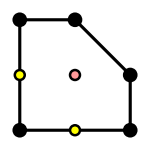

```mathematica
PdP2DefFieldChiralIdealByDegree[{2,2}]/.{Y[1]->X[0,1],Y[2]->X[-1,1],Y[3]->X[0,0],Y[4]->X[-1,0],Y[5]->X[1,0],Y[6]->X[1,-1],Y[7]->X[0,-1],Y[8]->X[-1,-1]}
Values@{Y[1]->X[0,1],Y[2]->X[-1,1],Y[3]->X[0,0],Y[4]->X[-1,0],Y[5]->X[1,0],Y[6]->X[1,-1],Y[7]->X[0,-1],Y[8]->X[-1,-1]}/.X->List//PolytopePlot[#,ImageSize->150]&
```

```mathematica
PdP2DefFieldChiralIdealNewByDegree[{2,2}]/.{Y[1]->X[0,1],Y[2]->X[-1,1],Y[3]->X[0,0],Y[4]->X[-1,0],Y[5]->X[1,0],Y[6]->X[1,-1],Y[7]->X[0,-1],Y[8]->X[-1,-1]}
Values@{Y[1]->X[0,1],Y[2]->X[-1,1],Y[3]->X[0,0],Y[4]->X[-1,0],Y[5]->X[1,0],Y[6]->X[1,-1],Y[7]->X[0,-1],Y[8]->X[-1,-1]}/.X->List//PolytopePlot[#,ImageSize->150]&
```

{X[-1,1] X[0,0]-X[-1,0] X[0,1],X[0,0] X[0,1]-X[-1,1] X[1,0],-X[0,1] X[1,-1]+X[0,0] X[1,0],X[0,0]^2-X[0,-1] X[0,1],-X[0,-1] X[0,1]+X[-1,0] X[1,0],-X[0,-1] X[0,1]+X[-1,1] X[1,-1],X[0,0] X[1,-1]-X[0,-1] X[1,0],X[-1,0] X[0,0]-X[-1,-1] X[0,1],X[-1,1] X[0,-1]-X[-1,-1] X[0,1],X[-1,0]^2-X[-1,-1] X[-1,1],X[-1,0] X[0,-1]-X[-1,-1] X[0,0],X[-1,0] X[1,-1]-X[-1,-1] X[1,0],X[0,-1] X[0,0]-X[-1,-1] X[1,0],X[0,-1]^2-X[-1,-1] X[1,-1]}

-Graphics-

## Resolutions Flow

### PdP_2 ⟹ dP_2 (a)

#### Deformation 1: (1→2→1) – (3→4→5→3)

```mathematica
kcTablePdP2=KahlerChambersCompatibility[WPdP2,"ShowProgress"->True];
kcTabledP2A=KahlerChambersCompatibility[WdP2AFromDef1,"ShowProgress"->True];
kcFlowPdP2dP2A=KahlerChambersFlowGraph[kcTablePdP2,kcTabledP2A,"ShowProgress"->True]
```

-Graphics-

```mathematica
equalGraphPdP2dP2A=Apply[UndirectedEdge]@*VertexList/@Select[IsomorphicGraphQ[CycleGraph[2,DirectedEdges->True],#]&]@WeaklyConnectedGraphComponents@kcFlowPdP2dP2A;
nonequalGraphPdP2dP2A=Select[Not@IsomorphicGraphQ[CycleGraph[2,DirectedEdges->True],#]&]@WeaklyConnectedGraphComponents@kcFlowPdP2dP2A;
```

```mathematica
Graph[#,GraphLayout->"LayeredEmbedding"]&/@Join[
GroupBy[EdgeList@Graph[Splice@*EdgeList/@nonequalGraphPdP2dP2A],
MapAt[{pqWebPlot[TransformedMesh[{{0,1},{1,0}}]@#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None],pqWebPlot[TransformedMesh[{{0,1},{1,-1}}]@#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None]}&,{2}]@*MapAt[(pqWebPlot[#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None]&),{1}]@*Apply[DirectedEdge]@*Map[First]->Apply[DirectedEdge]@*Map[Last]
],
GroupBy[EdgeList@equalGraphPdP2dP2A,
MapAt[{pqWebPlot[TransformedMesh[{{0,1},{1,0}}]@#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None],pqWebPlot[TransformedMesh[{{0,1},{1,-1}}]@#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None]}&,{2}]@*MapAt[(pqWebPlot[#,ImageSize->{Automatic,150},]&),{1}]@*Sort@*Apply[UndirectedEdge]@*Map[First]->Apply[UndirectedEdge]@*Map[Last]
]
]//Grid[KeyValueMap[List]@#,Frame->All,ItemSize->{{All,Automatic},Automatic}]&;
Export[FileNameJoin[{$FiguresDirectory,"kcFlowGraph_PdP2_dP2PhaseA.pdf"}],%];
```

## Resolutions Volumes

### PdP_2 ⟹ dP_2 (a)

#### Deformation 1: (1→2→1) – (3→4→5→3)

```mathematica
kvTbPdP2=KahlerVolumes[WPdP2,"ShowProgress"->True];
kvTbdP2A=KahlerVolumes[WdP2AFromDef1,"ShowProgress"->True];
```

```mathematica
tM={{-1,1},{0,1}};
polytVolPdP2dP2A=volumesTable[
MapAt[KeyMap[x↦tM.x],{All,-1,2}]@MapAt[TransformedMesh[tM],{All,-1,1}]@Map[ReverseSortBy@First]@WeaklyConnectedComponents[kcFlowPdP2dP2A],
{kvTbPdP2,Map[
KeyMap[KeyMap[x↦tM.x]]@*Map[KeyMap[x↦x.Transpose[tM]]],
KeyMap[TransformedMesh[tM]]@kvTbdP2A]}
];
```

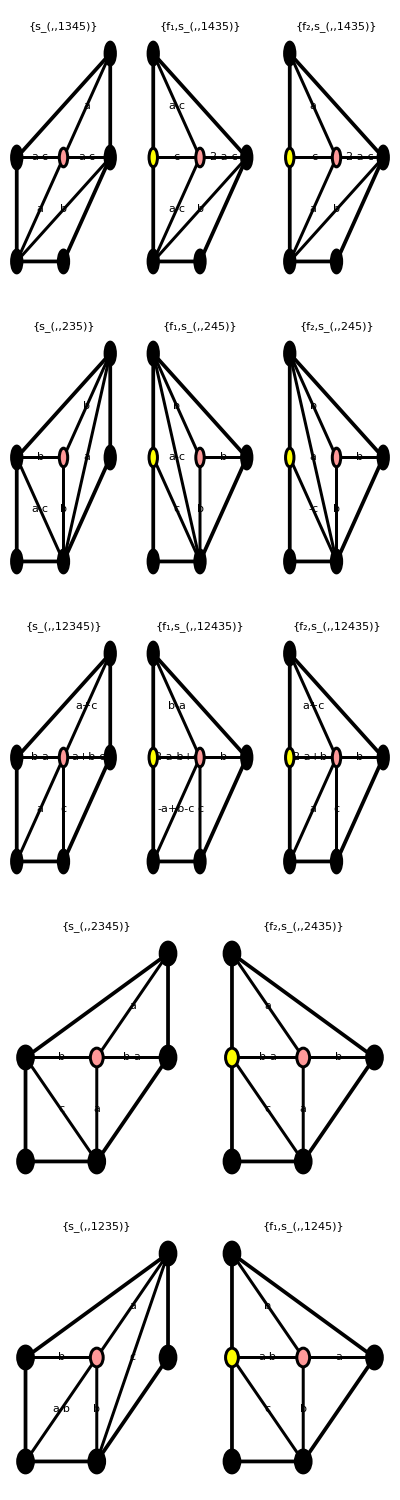

```mathematica
KeyValueMap[
{k,v}↦MapThread[PolytopePlot[#1,"PolytopeCellLabel"->Normal[(Style[#,Background->LightBlue]&)/@#2],PlotLabel->#3]&,{Splice@Transpose@k,First@v}],
polytVolPdP2dP2A
]//ReverseSortBy[Length]//Map[GraphicsRow]//Column
```